```mathematica
Time-dependent LZ spectrum
```

```mathematica
Clear[alphaMas, alphaMenos, alphaZ, Ω, β]
```

```mathematica
β = 0.2; Ω = 0.4;
```

```mathematica
ecuacionesOptimizadas={x'[t]==I*((Ω/2)*x[t]-(β^2/2)*t)*x[t]*2-(I*Ω/2)*(1+x[t]^2),y'[t]==(I/2)*(Ω*x[t]-(β^2)*t),z'[t]==-(I*Ω/2)*Exp[2*y[t]],x[-160]==0,y[-160]==0,z[-160]==0};
```

```mathematica
{alphaMas, alphaZ, alphaMenos}=NDSolveValue[ecuacionesOptimizadas,{x,y, z},{t,-250, 250},AccuracyGoal->10, PrecisionGoal->10];
```

### Transition Probabilities

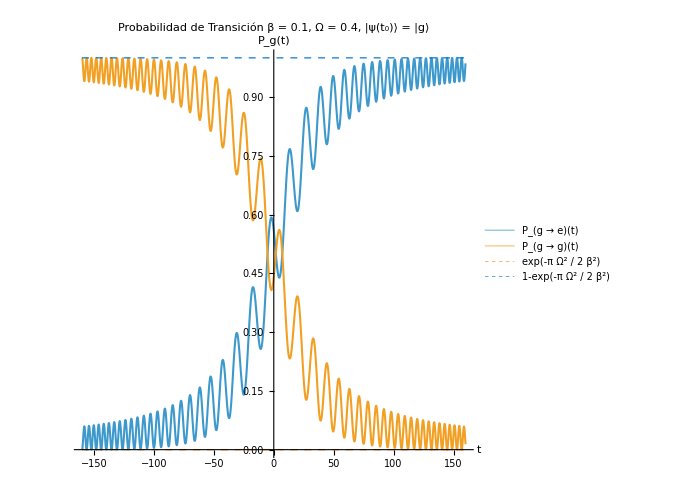

```mathematica
Plot[{(Abs[alphaMas[t]]^2 )Exp[-2Re[alphaZ[t]]], Abs[Exp[- alphaZ[t]] ]^2,Exp[-π(Ω^2/(2(β^2)))], 1- Exp[-π(Ω^2/(2β^2))]}, {t, -160, 160}, FrameTicksStyle->{{20,2},{20,20}}, PlotStyle->{Thickness[0.003], Thickness[0.003], Directive[Dashed, Thickness[0.002], Orange, Opacity[0.85]], Directive[Dashed, Thickness[0.002], RGBColor[0,0.45,0.8], Opacity[0.85]]},PlotLegends-> {"P_(g → e)(t)", "P_(g → g)(t)","exp(-π Ω^2 / 2 β^2)","1-exp(-π Ω^2 / 2 β^2)"},AxesLabel-> {Style["t",14,GrayLevel[0.26]] , Style["P_g(t)",13, GrayLevel[0.26]]},AspectRatio->1, ImageSize->500,
PlotLabel->Style["Probabilidad de Transición  β = 0.1, Ω = 0.4, |ψ(t_0)⟩ = |g⟩ ", 18, FontFamily->"Times New Roman", Black]]
```

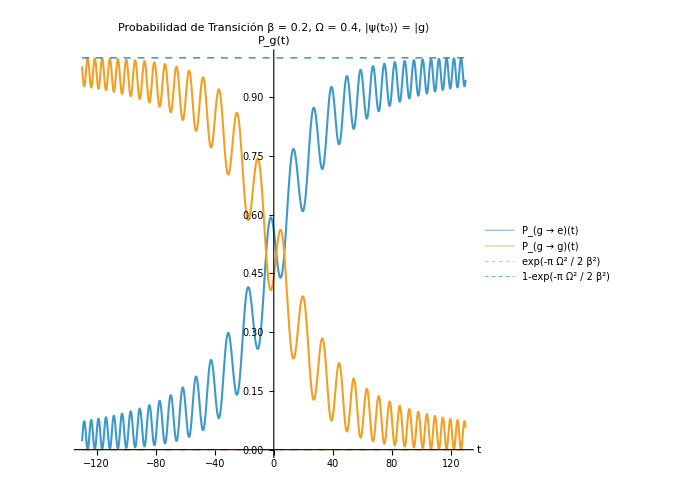

```mathematica
Plot[{(Abs[alphaMas[t]]^2 )Exp[-2Re[alphaZ[t]]], Abs[Exp[- alphaZ[t]] ]^2,Exp[-π(Ω^2/(2(β^2)))], 1- Exp[-π(Ω^2/(2β^2))]}, {t, -130, 130}, FrameTicksStyle->{{20,2},{20,20}}, PlotStyle->{Thickness[0.003], Thickness[0.003], Directive[Dashed, Thickness[0.002], Orange, Opacity[0.85]], Directive[Dashed, Thickness[0.002], RGBColor[0,0.45,0.8], Opacity[0.85]]},PlotLegends-> {"P_(g → e)(t)", "P_(g → g)(t)","exp(-π Ω^2 / 2 β^2)","1-exp(-π Ω^2 / 2 β^2)"},AxesLabel-> {Style["t",14,GrayLevel[0.26]] , Style["P_g(t)",13, GrayLevel[0.26]]},AspectRatio->1, ImageSize->500,
PlotLabel->Style["Probabilidad de Transición  β = 0.2, Ω = 0.4, |ψ(t_0)⟩ = |g⟩ ", 18, FontFamily->"Times New Roman", Black]]
```

### Energy Levels

```mathematica
del[T_]:= T β^2;
```

```mathematica
Emas[T_, Ω_]:=1/2 Sqrt[Ω^2 +del[T]^2]
```

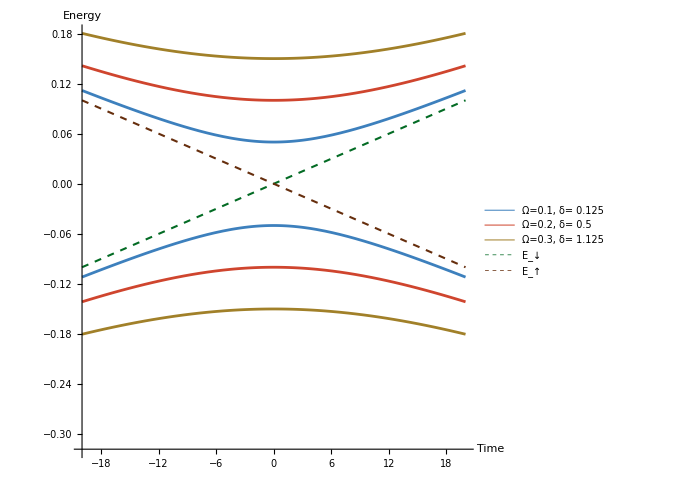

```mathematica
Plot[{Emas[t, 0.1],Emas[t, 0.2] ,Emas[t, 0.3],1/2 del[t],-1/2 del[t], -Emas[t,0.3],-Emas[t,0.2], -Emas[t,0.1]}, {t, -20, 20}, FrameTicksStyle->{{20,2},{20,20}}, PlotStyle->{Directive[Thickness[0.004], RGBColor[0.24,0.5,0.74]],Directive[Thickness[0.004], RGBColor[0.81,0.27,0.18]],Directive[Thickness[0.004], RGBColor[0.63,0.5,0.16]],Directive[Thickness[0.003], Dashed, RGBColor[0.01,0.42,0.14]],Directive[Thickness[0.003], Dashed, RGBColor[0.4,0.18,0.05]],Directive[Thickness[0.004], RGBColor[0.63,0.5,0.16]] ,
Directive[Thickness[0.004], RGBColor[0.81,0.27,0.18]],Directive[Thickness[0.004], RGBColor[0.24,0.5,0.74]]},
PlotLegends->{Style["Ω=0.1, δ= 0.125"], Style["Ω=0.2, δ= 0.5"], Style["Ω=0.3, δ= 1.125"] , Style["E_↓",RGBColor[0.01,0.42,0.14] ],Style["E_↑",RGBColor[0.4,0.18,0.05] ] },AxesOrigin->{-20,-0.318},
AxesLabel-> {Style["Time",16,GrayLevel[0.26]] , Style["Energy",16, GrayLevel[0.26]]}, AspectRatio->1, ImageSize->500]
```

### Spectrum Integrals

```mathematica
I1[Γ_?NumericQ, ω_?NumericQ, T_?NumericQ, T0_?NumericQ]:= Abs[NIntegrate[-Exp[(Γ-I ω)t]Exp[-2 alphaZ[t]]alphaMenos[t]^2, {t,T0 , T}, MaxRecursion->20, Method->"LevinRule"]]^2
```

```mathematica
I2[Γ_?NumericQ, ω_?NumericQ, T_?NumericQ, T0_?NumericQ]:= Abs[NIntegrate[-Exp[(Γ-I ω)t]Exp[-2alphaZ[t]]alphaMenos[t],{t,T0,T}, MaxRecursion->20, Method->"LevinRule"]]^2
```

```mathematica
S[Γ_?NumericQ,ω_?NumericQ,T_?NumericQ, T0_?NumericQ]:=2Γ Exp[-2Γ T](I1[Γ, ω,T, T0]+I2[Γ, ω,T,T0])
```

```mathematica
step = 0.03;Γ = 0.1;T0=-200;
```

```mathematica
I1[Γ_, ω_, T_, T0_]:= Abs[NIntegrate[-Exp[(Γ-I ω)t]Exp[-2 alphaZ[t]]alphaMenos[t]^2, {t,T0 , T}, MaxRecursion->20]]^2
```

```mathematica
I2[Γ_, ω_, T_, T0_]:= Abs[NIntegrate[-Exp[(Γ-I ω)t]Exp[-2alphaZ[t]]alphaMenos[t],{t,T0,T}, MaxRecursion->20]]^2
```

```mathematica
S[Γ_,ω_,T_, T0_]:=2Γ Exp[-2Γ T](I1[Γ, ω,T, T0]+I2[Γ, ω,T,T0])
```

### TDS Initial ground state

```mathematica
Γ = 0.1;T0=-180;
```

## Graficos: Evolución temporal del espectro usando varias trazas

### Datos con conjuntos de trazas

En datos3D se tiene una lista de listas, donde cada sublista es una curva en el tiempo t correcto, con formato {x, y, z} (frecuencia, tiempo, amplitud).

```mathematica
step = 0.03;
```

```mathematica
(*Definimos la lista exacta de instantes de tiempo*)
tiempos1={-200,-140,-100, -60,-50,-40,-30,-20};
(*Generamos todas las trazas de una sola vez. insertamos't' directamente como la segunda coordenada (eje y) *)
datos3D1=ParallelTable[Table[{v,t,S[Γ,v,t,T0]},{v,-1.4,1.4,step}],{t,tiempos1}];
```

```mathematica
tiempos2={-15,-10,-5,0,5,10,15,20};
datos3D2=ParallelTable[Table[{v,t,S[Γ,v,t,T0]},{v,-1.4,1.4,step}],{t,tiempos2}];
```

```mathematica
tiempos3={30,40,50,60,80,100,120,140};
datos3D3=ParallelTable[Table[{v,t,S[Γ,v,t,T0]},{v,-1.0,1.8,step}],{t,tiempos3}];
```

```mathematica
tiempos={-100, -80, -70, -60,-50,-30,-20,-16,-12,-8,-4,0,4,8,12,16,20,30,50,70,80,100};
datos3D=ParallelTable[Table[{v,t,S[Γ,v,t,T0]},{v,-0.8,2.4,step}],{t,tiempos}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small. will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of Further output of `1` will be suppressed during this calculation. will be suppressed during this calculation.

### Paletas de colores

```mathematica
(*Definimos una paleta de 11 colores basada en un degradado*)
paletaTiempo=Table[Blend[{RGBColor[0.1,0.2,0.6],RGBColor[0.5,0.1,0.5],RGBColor[0.8,0.2,0.2]},i/10],{i,0,21}];
(*paletaTiempo=Table[Blend[{RGBColor[0.1,0.2,0.6],RGBColor[0.5,0.1,0.5],RGBColor[0.8,0.2,0.2]},i/10],{i,0,10}];*)
paletaMagma=Table[Blend[{Black,Purple,RGBColor[0.8,0.2,0.2],Orange},i/10],{i,0,10}];
paletaOceano=Table[Blend[{RGBColor[0.1,0.1,0.4],RGBColor[0.2,0.6,0.6],RGBColor[0.9,0.8,0.2]},i/10],{i,0,10}];
paletaSunset=Table[ColorData["SunsetColors"][i/10],{i,0,10}];
paletaMonocromatica=Table[Blend[{RGBColor[0.05,0.1,0.25],RGBColor[0.6,0.7,0.85]},i/10],{i,0,10}];
```

### Grafico de cascada (Trazas equispaciadas)

```mathematica
(*Altura de la base para el sombreado*)
zBase=0;

(*Generamos automáticamente los Ticks del eje Y asociando cada índice entero con la cadena de texto de su tiempo real correspondiente*)
ticksY=Table[{i,Style[ToString[tiempos[[i]]],12]},{i,1,Length[tiempos]}];

grafico3DSombreadoEquispaciado=Style[Show[Graphics3D[Table[Module[{puntosOriginales,puntos,ptInicial,ptFinal,puntosPoligono,colorTraza},
(*1. Extraemos la lista de puntos {v,t,S} original*)
puntosOriginales=datos3D[[i]];
(*2. Mapeamos la lista sustituyendo la coordenada y (tiempo real) por el índice entero'i'.Cada punto pasa de {v,t,S} a {v,i,S}*)
puntos=Map[{#[[1]],i,#[[3]]}&,puntosOriginales];
(*3. Identificamos los extremos en la nueva escala indexada*)
ptInicial=puntos[[1]];
ptFinal=puntos[[-1]];
(*4. Cerramos la curva para el polígono usando el índice'i' fijo para el eje y*)
puntosPoligono=Join[puntos,{{ptFinal[[1]],i,zBase},{ptInicial[[1]],i,zBase}}];
(*5. Definimos el color gradiente continuo*)
colorTraza=ColorData["SunsetColors"][i/Length[datos3D]];
{
(*EL ÁREA SOMBREADA*)
EdgeForm[None],FaceForm[Directive[colorTraza,Opacity[0.4]]],Polygon[puntosPoligono],
(*LA CURVA SUPERIOR (TRAZA)*)
Darker[colorTraza,0.4],AbsoluteThickness[1.5],Line[puntos]
}
],
(*Recorremos todas las trazas de datos3D*)
{i,1,Length[datos3D]}]
],
(*---CONFIGURACIÓN DE EJES Y ESTÉTICA---*)
Axes->{True, True, False},
(*El rango de Y ahora va estrictamente desde 1 hasta el número total de trazas*)
PlotRange->{All,{1,Length[datos3D]}, {-0.2,11.2}},
(*Mantenemos tus ejes estáticos fijos:X enfrente,Y a la derecha,Z atrás*)
AxesEdge->{{-1,-1},{1,-1},{-1,1}},BoxRatios->{1,1.5,0.6},Boxed->False,
(*Inyectamos los Ticks personalizados en el eje Y para engañar al ojo humano*)
Ticks->{Automatic,ticksY,Automatic},BaseStyle->{FontFamily->"Times New Roman",FontSize->12,Black},
TicksStyle->Directive[FontSize->12,Black],Lighting->"Neutral",
AxesLabel->{Style["ω",FontSize->16,Italic],Style["t",FontSize->16,Italic],Style["S",FontSize->16,Italic]},
ImageSize->500,Antialiasing->True,
ViewProjection->"Orthographic"]]
```

-Graphics3D-

#### Ejemplos

```mathematica
-Graphics3D--Graphics3D-
```

```mathematica
-Graphics3D--Graphics3D--Graphics3D-
```

```mathematica
-Graphics3D--Graphics3D--Graphics3D-
```

```mathematica
-Graphics3D--Graphics3D-
```

```mathematica
-Graphics3D--Graphics3D-
```

### Grafico de cascada (Eje con Tiempo real)

```mathematica
(* Altura de la base para el sombreado *)
zBase = 0;

grafico3DSombreado = Style[
  Show[
    Graphics3D[
      Table[
        Module[{puntos, ptInicial, ptFinal, puntosPoligono, colorTraza},
         
         (* 1. Extraemos los puntos de la traza actual directamente de datos3D *)
         puntos = datos3D3[[i]];
         
         (* 2. Identificamos los extremos para proyectarlos al suelo *)
         ptInicial = puntos[[1]];
         ptFinal = puntos[[-1]];
         
         (* 3. Cerramos la curva para el polígono. 
            Como 'puntos' ya tiene el tiempo físico en la coordenada y, esto funciona directo *)
         puntosPoligono = Join[
           puntos, 
           {{ptFinal[[1]], ptFinal[[2]], zBase}, {ptInicial[[1]], ptInicial[[2]], zBase}}
         ];
         
         (* 4. Definimos el color de forma dinámica según la posición de la traza *)
         colorTraza = ColorData["SunsetColors"][i / Length[datos3D3]];
         
         {
          (* EL ÁREA SOMBREADA *)
          EdgeForm[None],
          FaceForm[Directive[colorTraza, Opacity[0.4]]], 
          Polygon[puntosPoligono],
          
          (* LA CURVA SUPERIOR (TRAZA) *)
          Darker[colorTraza, 0.4], 
          AbsoluteThickness[1.5],
          Line[puntos]
         }
        ], 
        (* Iteramos sobre la longitud total de la nueva lista unificada *)
        {i, 1, Length[datos3D3]}
      ]
    ],
    
    (* --- CONFIGURACIÓN DE EJES Y ESTÉTICA --- *)
    Axes -> {True, True, False},
    AxesEdge->{{-1,-1},{1,-1},{-1,1}},
PlotRange->{All, All, {-0.2,15.2}},
    BoxRatios -> {1, 1.5, 0.6},
    Boxed -> False,
    
    (* Los Ticks ahora pueden ser automáticos, o puedes pasar la lista 'tiempos' directamente *)
    Ticks->{Automatic,tiempos3,Automatic},
    
    BaseStyle -> {FontFamily -> "Times New Roman", FontSize -> 12, Black},
    TicksStyle -> Directive[FontSize -> 12, Black], 
    Lighting -> "Neutral",
    AxesLabel -> {Style["ω", FontSize -> 16, Italic], 
                  Style["t", FontSize -> 16, Italic], 
                  Style["S", FontSize -> 16, Italic]}, 
    ImageSize -> 500, 
    Antialiasing -> True,
    
    (* Recomendación: Proyección ortográfica para no distorsionar las alturas *)
    ViewProjection -> "Orthographic"
  ]
]
```

#### Ejemplos

```mathematica
-Graphics3D--Graphics3D--Graphics3D-
```

### Grafico 3D Mesh Grid

```mathematica
(*Transformamos la lista de trazas en una única lista continua de coordenadas*)
datosCompletos=Flatten[datos3D,1];
```

```mathematica
graficoSuperficie=ListPlot3D[datosCompletos,
(*---MALLA Y COLOR---*)
Mesh->{30,Length[tiempos]},
MeshStyle->Directive[Opacity[0.4],
GrayLevel[0.2]],ColorFunction->"Rainbow",
(*---CONFIGURACIÓN DE EJES Y ESTÉTICA---*)
Axes->{True, True, False},
AxesLabel->{Style["ω",16,Italic],Style["t",16,Italic],Style["S",16,Italic]},
LabelStyle->Directive[Black,FontFamily->"Times New Roman",FontSize->12],Boxed->False,PlotRange->All,
(*Fijamos los ejes*)
AxesEdge->{{-1,-1},{1,-1},{-1,1}},
ImageSize->Large,
(*Mejora el renderizado de la superficie*)
MaxPlotPoints->100]
```

-Graphics3D-

```mathematica
-Graphics3D--Graphics3D-
```

#### Ejemplos

```mathematica
-Graphics3D--Graphics3D-
```

### 2D Density Plot

```mathematica
(*1. Definimos un umbral mínimo para evitar el error de Log10[0].Un valor de 10^-6 o 10^-8 suele ser ideal.*)
epsilon=10^-6;
```

```mathematica
(*Transformamos la lista de trazas en una única lista continua de coordenadas*)
datosCompletos=Flatten[datos3D,1];
```

```mathematica
(*2. Transformamos la lista plana.A la coordenada z (Amplitud S) le aplicamos el Logaritmo en base 10*)
datosCompletosLog=Map[{#[[1]],#[[2]],Log10[#[[3]]+epsilon]}&,datosCompletos];
```

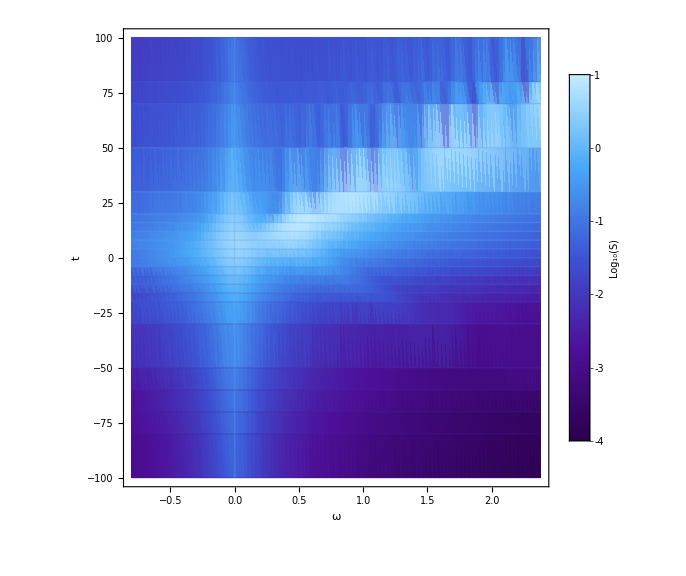

```mathematica
(*3. Generamos el Gráfico de Densidad con los nuevos datos*)
graficoDensidadLog=ListDensityPlot[datosCompletosLog,
(*---MALLA Y COLOR---*)
Mesh->{{0},tiempos},MeshStyle->Directive[Opacity[0.3],GrayLevel[0.1]],ColorFunction->"DeepSeaColors",

(*---CONFIGURACIÓN DE EJES Y ESTÉTICA---*)
PlotLegends->BarLegend[Automatic,LegendLabel->Style["\!\(\*SubscriptBox[\(Log\), \(10\)]\)(S)",14,Italic]],
Frame->True,FrameLabel->{Style["ω",16,Italic],Style["t",16,Italic]},
BaseStyle->{FontFamily->"Times New Roman",FontSize->12,Black},
TicksStyle->Directive[FontSize->12,Black],
(*Forzamos a que el renderizado muestre todo el rango logarítmico*)
PlotRange->All,
ImageSize->Large]
```

```mathematica
graficoDensidad2D=ListDensityPlot[datosCompletos,
(*---MALLA Y COLOR---*)
(*Forzamos una línea de malla sobre cada instante de tiempo real simluado*)
Mesh->{{0},tiempos},MeshStyle->Directive[Opacity[0.3],GrayLevel[0.1]],
ColorFunction->"SunsetColors",
(*---CONFIGURACIÓN DE EJES Y ESTÉTICA PROFESIONAL---*)
PlotLegends->Automatic,Frame->True,
FrameLabel->{Style["ω",16,Italic],Style["t",16,Italic]},
BaseStyle->{FontFamily->"Times New Roman",FontSize->12,Black},
TicksStyle->Directive[FontSize->12,Black],GridLines->{{0},tiempos},
PlotRange->All,ImageSize->Large]
```

#### Ejemplos

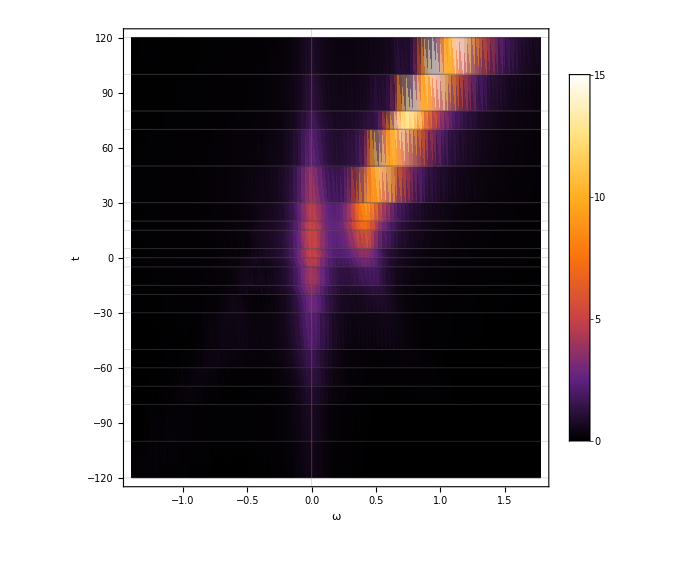
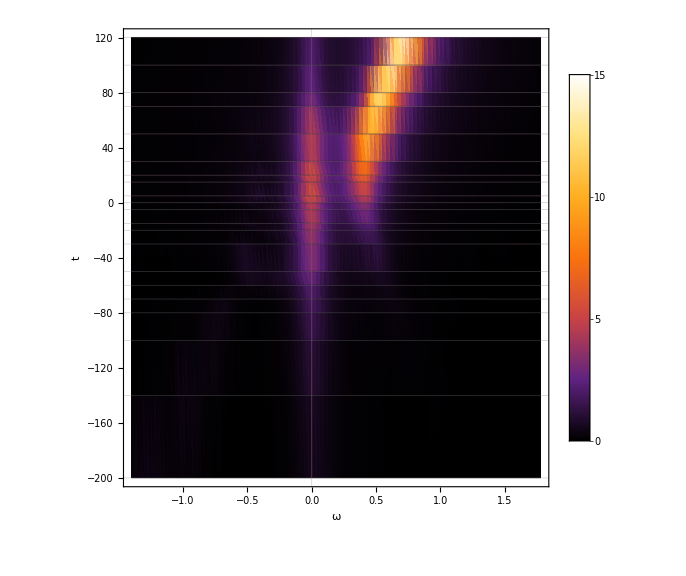

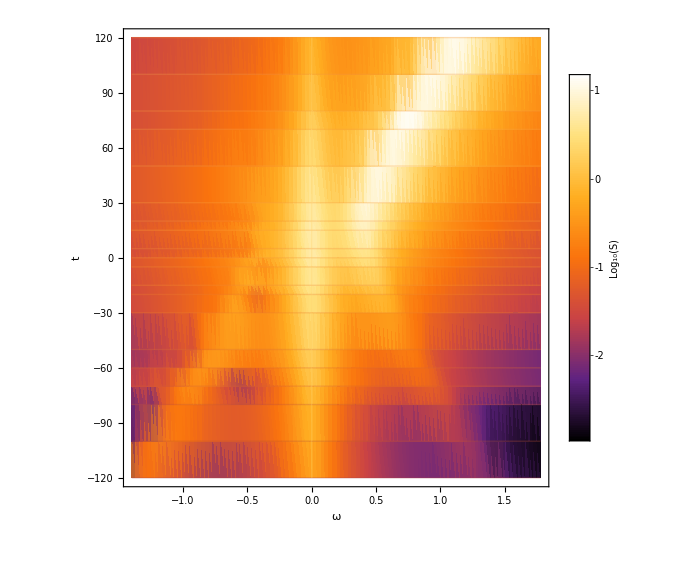
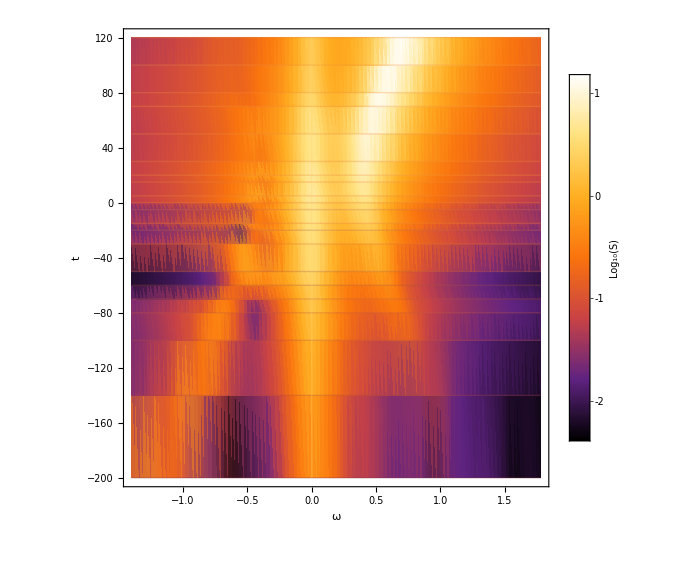

### 2D List Animation

```mathematica
(*Transformamos datos3D:cada punto {v,t,S} pasa a ser {v,S}*)
datos2DParaAnimacion=Map[#[[{1,3}]]&,datos3D,{2}];
```

```mathematica
(*---PASO I:GENERAR LA LISTA DE FOTOGRAMAS---*)
frames=Table[ListLinePlot[datos2DParaAnimacion[[i]],
(*Extraemos la traza 2D del instante i*)
(*---ESTÉTICA---*)
PlotStyle->{Directive[Thick,Darker[Blue]]},

(*---CONFIGURACIÓN CRÍTICA DE EJES---*)
(*Fijamos el rango para que la animación sea estable.Ajusta estos valores según los máximos y mínimos reales de tu simulación.*)
PlotRange->{{-1.5,1.9},{0,14.5}},
Frame->True,GridLines->Automatic,
FrameLabel->{Style["ω",16,Italic],Style["S",16,Italic]},
BaseStyle->{FontFamily->"Times New Roman",FontSize->12},
(*Mostramos el tiempo actual en el título de la gráfica*)
PlotLabel->Style[StringForm["t = ``",tiempos[[i]]],16,Black],
ImageSize->600],
{i,1,Length[tiempos]} (*Un fotograma por cada instante de tiempo*)];

(*---PASO II:CREAR LA ANIMACIÓN INTERACTIVA---*)
ListAnimate[frames,AnimationRate->2,ControlPlacement->Top]
```

### 2D Grafico de Cascada con vertical Off set

```mathematica
(*Posición X de las etiquetas.*)
xPosEtiquetas=-1.5;
```

```mathematica
(*1. Extraemos la amplitud máxima de TODO el conjunto de datos unificado*)
maxAmplitudGlobal=Max[datos2DParaAnimacion[[All,All,2]]];

(*2. Calculamos la altura máxima que necesitará el eje Y.Asume'n' como el número de trazas que pones en cada sub-gráfico (ej.8 o 9).*)
numTrazasPorSubGrafico=8;
alturaYMax=(numTrazasPorSubGrafico-1)*offsetVertical+maxAmplitudGlobal;

(*3. Definimos los límites fijos para el eje X (Frecuencia).
Asegúrate de que cubra desde tu etiqueta hasta el final del dominio.*)
rangoXGlobal={xPosEtiquetas-0.2,1.8}; 

(*4. Empaquetamos el PlotRange global*)
escalaGlobalFija={rangoXGlobal,{0,alturaYMax}};
```

```mathematica
datos2DParaAnimacion=Map[#[[{1,3}]]&,datos3D1,{2}];

(*---cuánto se desplaza cada traza hacia arriba respecto a la anterior.*)
offsetVertical=2.5;

graficoCascada2DConEtiquetas=Show[Table[Module[{datosTrazaOffset,colorTraza,etiquetaGrafica},
(*1. Calculamos el offset de la curva*)
datosTrazaOffset=Map[{#[[1]],#[[2]]+offsetVertical*(i-1)}&,datos2DParaAnimacion[[i]]];
(*2. Asignamos el color*)
colorTraza=ColorData["SunsetColors"][(i+0)/12];
(*3. CREACIÓN DE LA ETIQUETA DE TIEMPO*)(*Usamos Text para anclar la etiqueta a las coordenadas {x,y} exactas*)etiquetaGrafica=Graphics[Text[Style[StringForm["t = ``",tiempos1[[i]]],11,FontFamily->"Times New Roman",Black],{xPosEtiquetas,offsetVertical*(i-1)+0.7},{-1,0} (*Este vector {1,0} alinea el texto a la derecha del punto de anclaje*)]];
(*Devolvemos tanto la gráfica de la curva como el texto en una lista*){ListLinePlot[datosTrazaOffset,PlotStyle->Directive[Darker[colorTraza,0.4],AbsoluteThickness[1.5]],Filling->Axis,FillingStyle->Directive[colorTraza,Opacity[0.4]], AxesOrigin->{0,offsetVertical*(i-1)}, PlotRange->All],etiquetaGrafica}],{i,1,Length[tiempos1]}],
(*---CONFIGURACIÓN GLOBAL---*)
(*REEMPLAZO CRÍTICO:Usamos la escala matemática fija para que no haya estiramientos*)
PlotRange->escalaGlobalFija,
(*CRÍTICO:Añadimos un margen extra al gráfico a la izquierda para que Mathematica no recorte el texto de las etiquetas
PlotRangePadding->{{0.5,0.1},{Automatic,Automatic}},
*)
PlotRangePadding->None,
Axes->{True,False},
AxesLabel->{Style["ω",16,Italic],None},BaseStyle->{FontFamily->"Times New Roman",FontSize->12,Black},
TicksStyle->Directive[FontSize->12,Black],
ImageSize->500,AspectRatio->1]
```

#### Ejemplos

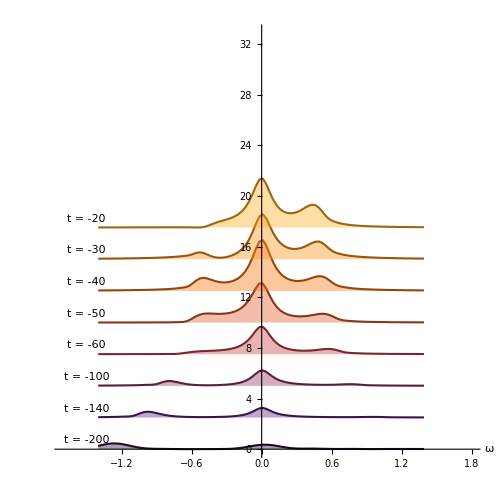
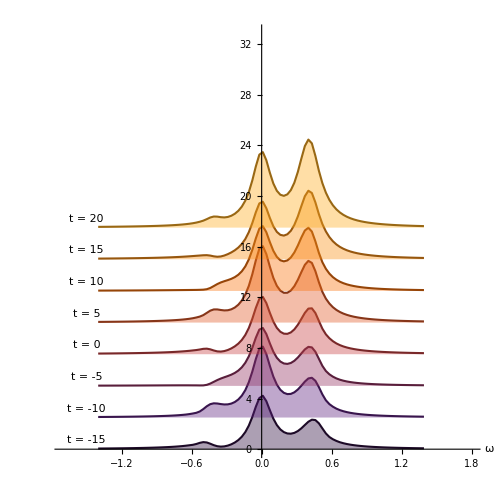
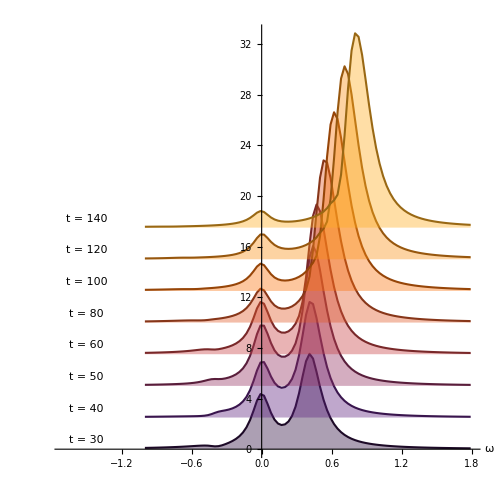

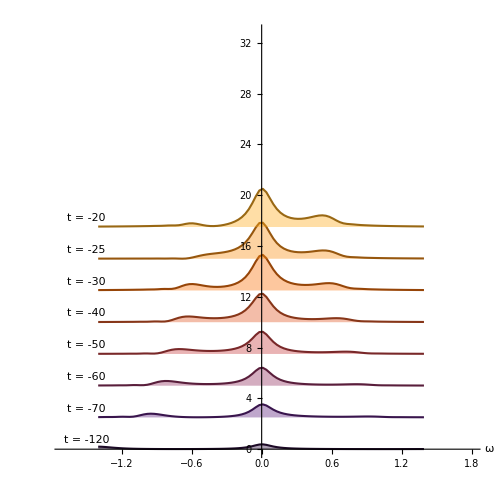
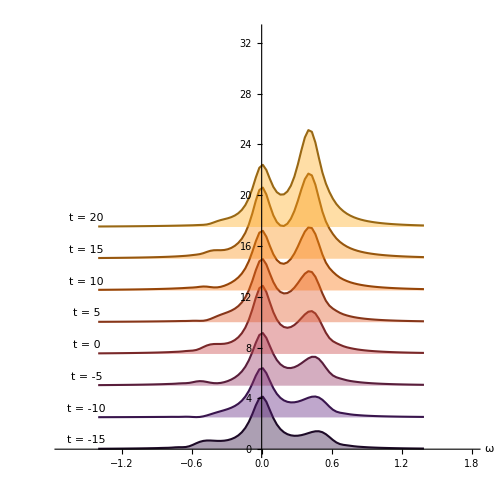
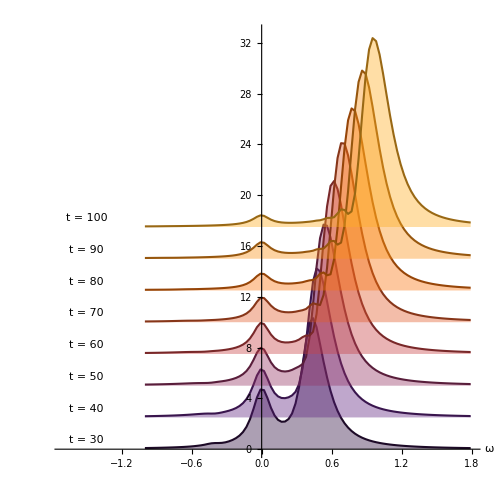

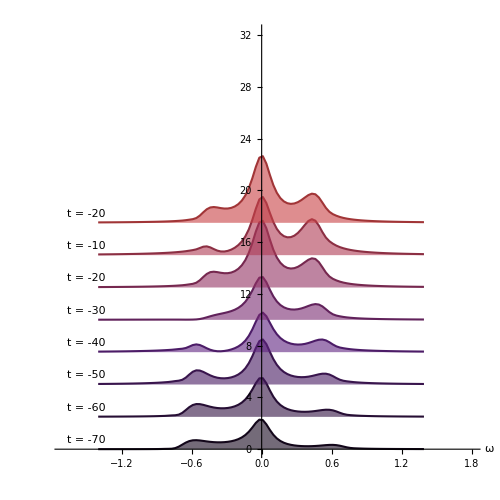
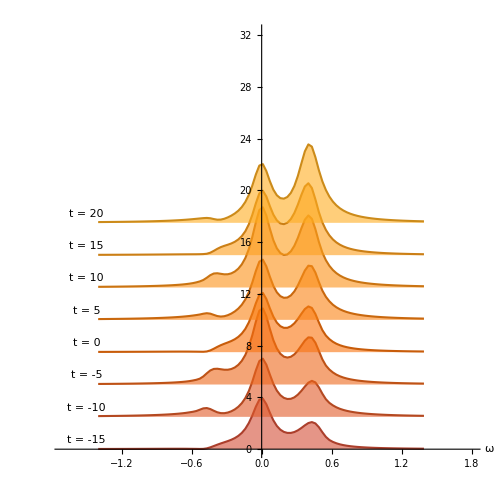

```mathematica
(*Transformamos datos3D:cada punto {v,t,S} pasa a ser {v,S}*)
datos2D1=Map[#[[{1,3}]]&,datos3D1,{2}];
datos2D2=Map[#[[{1,3}]]&,datos3D2,{2}];
datos2D3=Map[#[[{1,3}]]&,datos3D3,{2}];
datos2D  =Map[#[[{1,3}]]&,datos3D,{2}];
```

```mathematica
(*Añadimos un offset vertical para separar las líneas artificialmente*)
offset=3.2; 
datosConOffset=Table[Table[{punto[[1]],punto[[2]]+(i-1)*offset},{punto,datos2D[[i]]}],{i,1,Length[datos2D]}];

graficoLineasApiladas=ListLinePlot[datosConOffset,
PlotStyle->Table[Directive[paletaTiempo[[i]],AbsoluteThickness[1.2]],{i,1,12}],
PlotRange->{-0.2,38.0},Frame->False,Axes->{True, False},
Filling->{1->0,2->3.2,3->6.4,4->9.6,5->12.8,6->16.0,7->19.2,8->22.4,9->25.6,10->28.8,11->32.0},
(*Filling->{1->0,2->1.2,3->2.4,4->3.6,5->4.8,6->6.0,7->7.2,8->8.4,9->9.6,10->10.8,11->12.0,12->13.2,13->14.4,14->15.6,15->16.8,16->18.0,17->19.2,18->20.4,19->21.6, 20->22.8},*)
BaseStyle->{FontFamily->"Times New Roman",FontSize->10,Black},
FrameLabel->{Style["ω",Italic],Style["S(ω, t) + Offset",Italic]},
(*Colocamos etiquetas de texto al lado derecho de cada curva para indicar el tiempo*)Epilog->Table[Text[Style[ToString[tiempos[[i]]],FontSize->11,paletaTiempo[[i]]],{1.40,datos2D[[i]][[-1,2]]+(i-1)*offset},{1,-1}],{i,1,Length[tiempos]}],
ImageSize->600]
```

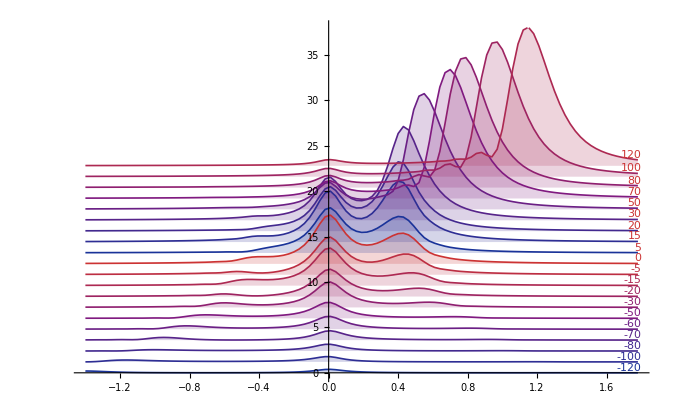
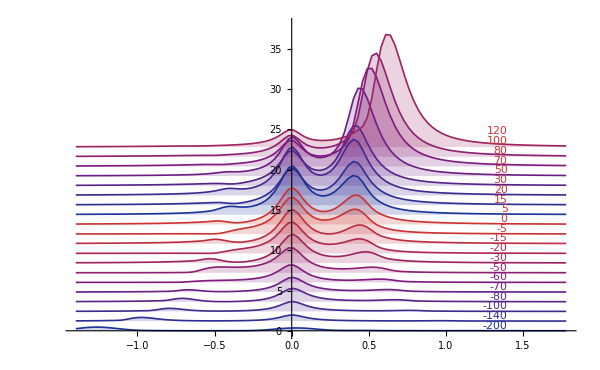

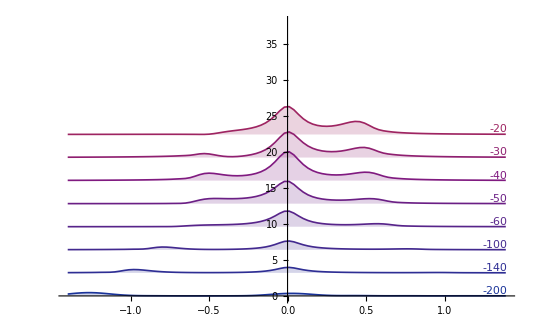
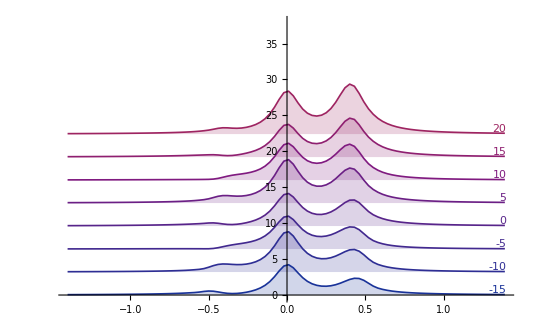
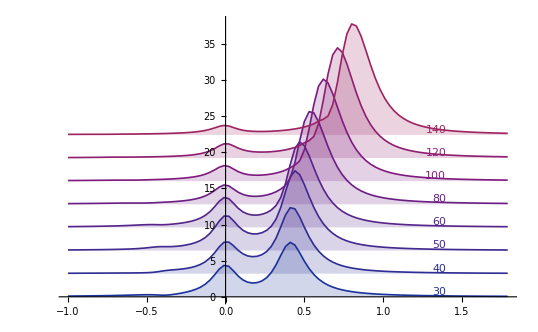

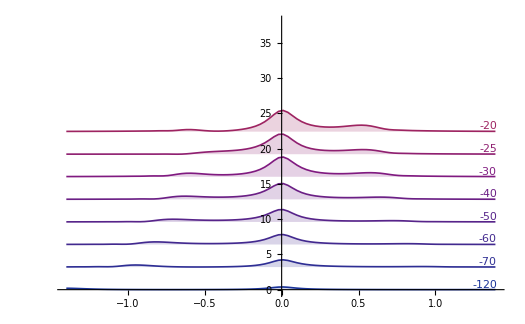
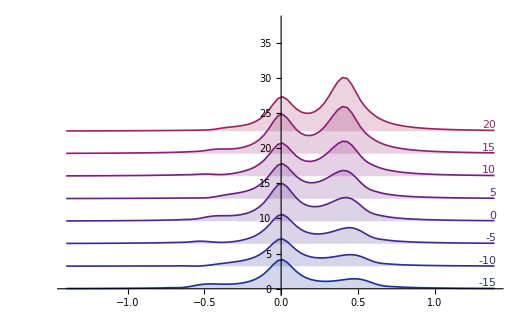
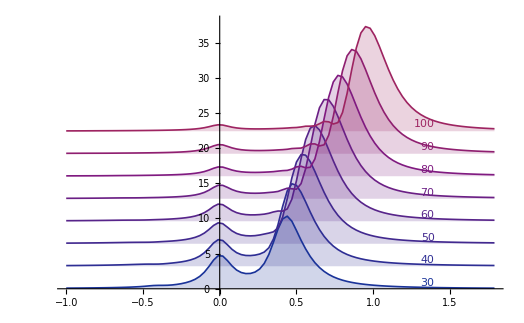

#### Spectrum Traces 3D Plot

```mathematica
DTrace01=ParallelTable[{ν,S[Γ,ν,-100,T0]},{ν,-1.4,1.4,0.03}];
DTrace02= ParallelTable[{ν,S[Γ,ν,-50,T0]},{ν,-1.4,1.4,0.03}];
DTrace03=ParallelTable[{ν,S[Γ,ν,-36,T0]},{ν,-1.4,1.4,0.03}];
DTrace04=  ParallelTable[{ν,S[Γ,ν,-24,T0]},{ν,-1.4,1.4,0.03}];
DTrace05=ParallelTable[{ν,S[Γ,ν,-8,T0]},{ν,-1.4,1.4,0.03}];
DTrace06=ParallelTable[{ν,S[Γ,ν,0,T0]},{ν,-1.4,1.4,0.03}];
DTrace07= ParallelTable[{ν,S[Γ,ν,8,T0]},{ν,-1.4,1.4,0.03}];
DTrace08=  ParallelTable[{ν,S[Γ,ν,24,T0]},{ν,-1.4,1.4,0.03}];
DTrace09=  ParallelTable[{ν,S[Γ,ν,36,T0]},{ν,-1.4,1.4,0.03}];DTrace10=ParallelTable[{ν,S[Γ,ν,80,T0]},{ν,-1.4,1.4,0.03}];DTrace11=ParallelTable[{ν,S[Γ,ν,120,T0]},{ν,-1.4,1.4,0.03}];
```

```mathematica
Trace01=Table[Insert[DTrace01[[j]],1,2],{j,1,Length[DTrace01]}];
Trace02=Table[Insert[DTrace02[[j]],2,2],{j,1,Length[DTrace02]}];
Trace03=Table[Insert[DTrace03[[j]],3,2],{j,1,Length[DTrace03]}];
Trace04=Table[Insert[DTrace04[[j]],4,2],{j,1,Length[DTrace04]}];
Trace05=Table[Insert[DTrace05[[j]],5,2],{j,1,Length[DTrace05]}];
Trace06=Table[Insert[DTrace06[[j]],6,2],{j,1,Length[DTrace06]}];
Trace07=Table[Insert[DTrace07[[j]],7,2],{j,1,Length[DTrace07]}];
Trace08=Table[Insert[DTrace08[[j]],8,2],{j,1,Length[DTrace08]}];
Trace09=Table[Insert[DTrace09[[j]],9,2],{j,1,Length[DTrace09]}];
Trace10=Table[Insert[DTrace10[[j]],10,2],{j,1,Length[DTrace10]}];
Trace11=Table[Insert[DTrace11[[j]],11,2],{j,1,Length[DTrace11]}];
```

```mathematica
grafico3d =Show[Graphics3D[{
Red,Thickness[0.0025],Opacity[0.6],BSplineCurve[Trace01],
Black,Thickness[0.0025],Opacity[0.6],BSplineCurve[Trace02],
RGBColor[0,0.8,0.8],Thickness[0.0025],Opacity[0.6],BSplineCurve[Trace03],
Purple,Thickness[0.0025],Opacity[0.6],BSplineCurve[Trace04],
RGBColor[0,0.7,0.4],Thickness[0.0025],Opacity[0.6],BSplineCurve[Trace05],
Orange,Thickness[0.0025],BSplineCurve[Trace06],
Purple,Thickness[0.0025],Opacity[0.6],BSplineCurve[Trace07],
Black,Thickness[0.0025],Opacity[0.6],BSplineCurve[Trace09],
Blue,Thickness[0.0025],Opacity[0.6],BSplineCurve[Trace08],
Red,Thickness[0.0025],Opacity[0.6],BSplineCurve[Trace10],
Green,Thickness[0.0025],Opacity[0.6],BSplineCurve[Trace11]
}],
Axes->{True,True,True},PlotRange->All,
Ticks->{Automatic,{{1,-100},{2,-50},{3,-36},{4,-24}{5,-8},{6,0},{7,8},{8,24}, {9, 36}, {10,80}, {11,120}},None},
TicksStyle->Directive[12,Black],BoxRatios->{3,5.5,2},
Boxed->False,AxesEdge->{{0,0},{1,0},{1,1}},ImageSize->700, AxesLabel->{
Style["ω_0",20,Black,FontFamily->"Times New Roman"],
Style["t",20,Black,FontFamily->"Times New Roman"]}];
grafico3d
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
Options[grafico3d,{ViewPoint,ViewVertical,ViewCenter,ViewAngle}]
```

{ViewPoint→{1.3,-2.4,2.},ViewVertical→{0,0,1},ViewCenter→Automatic,ViewAngle→Automatic}

#### Spectrum Traces 2D Plot

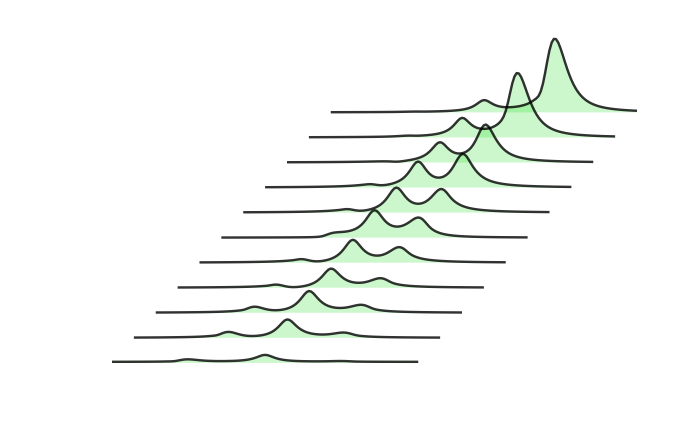

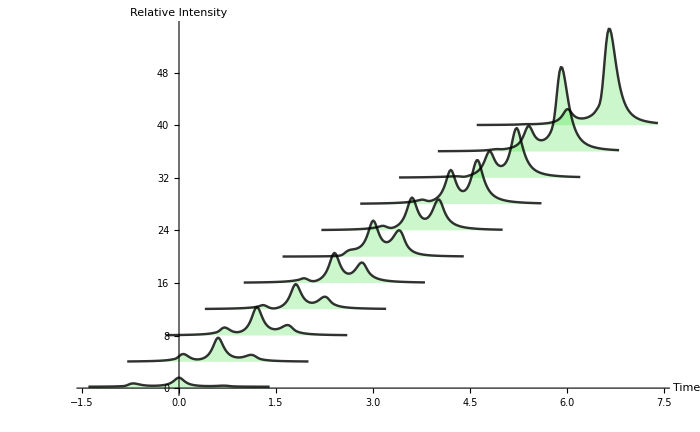

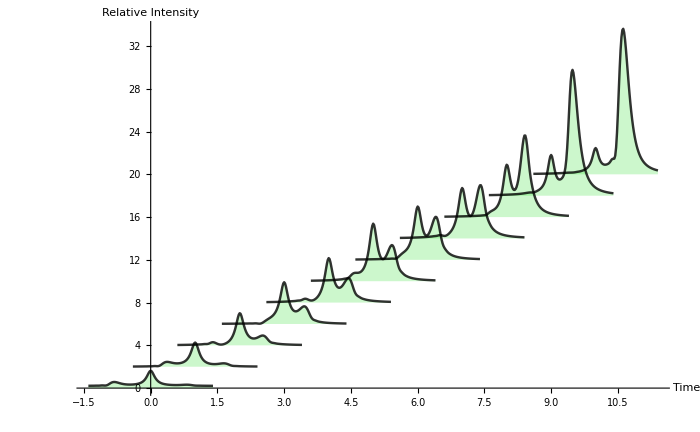

```mathematica
ListLinePlot[{
TranslationTransform[{0,0.2}][DTrace01],
TranslationTransform[{0.2,6}][DTrace02],
TranslationTransform[{0.4,12}][DTrace03],
TranslationTransform[{0.6,18}][DTrace04],
TranslationTransform[{0.8,24}][DTrace05],
TranslationTransform[{1.0,30}][DTrace06],
TranslationTransform[{1.2,36}][DTrace07],
TranslationTransform[{1.4,42}][DTrace08],
TranslationTransform[{1.6,48}][DTrace09],
TranslationTransform[{1.8,54}][DTrace10],
TranslationTransform[{2.0,60}][DTrace11]},
PlotStyle-> {Directive[Black, Thickness[0.0025],Opacity[0.8]]},
Filling->{1->0,2->5,3->10,4->15,5->20,6->25,7->30,8->35,9->40,10->45,11->50},
FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]],
Axes->{False,False},AxesLabel->{"Time","Relative Intensity"},ImageSize->700]
```

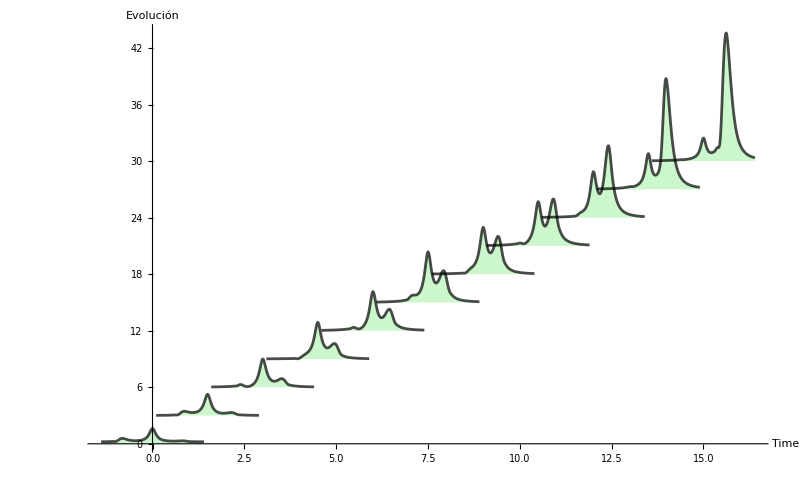

```mathematica
ListLinePlot[{
TranslationTransform[{15,30}][DTrace11],
TranslationTransform[{13.5,27}][DTrace10],
TranslationTransform[{12,24}][DTrace09],
TranslationTransform[{10.5,21}][DTrace08],
TranslationTransform[{9,18}][DTrace07],
TranslationTransform[{7.5,15}][DTrace06],
TranslationTransform[{6,12}][DTrace05],
TranslationTransform[{4.5,9}][DTrace04],
TranslationTransform[{3.0,6}][DTrace03],
TranslationTransform[{1.5,3}][DTrace02],
TranslationTransform[{0,0.2}][DTrace01]},
PlotStyle->Directive[ Black,Thickness[0.0025],Opacity[0.7]],Filling->{1->30,2->27,3->24,4->21,5->18,6->15,7->12,8->9,9->6,10->3,11->0},FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]],Axes->{True,False},AxesLabel->{"Time","Relative Intensity"},ImageSize->800]
```

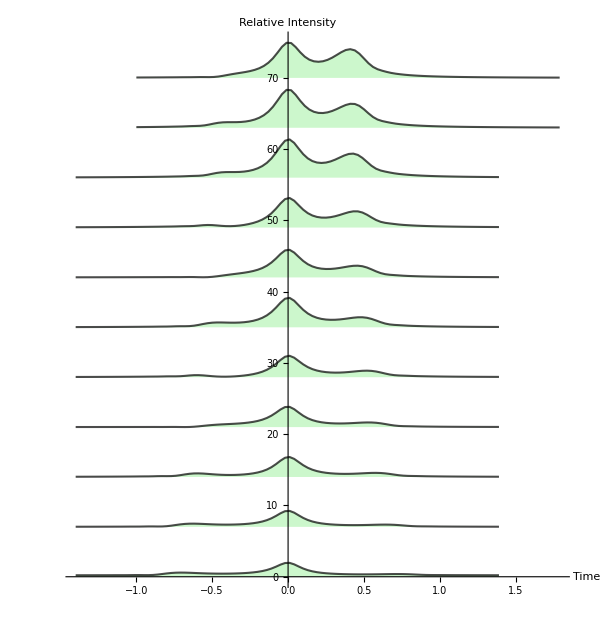

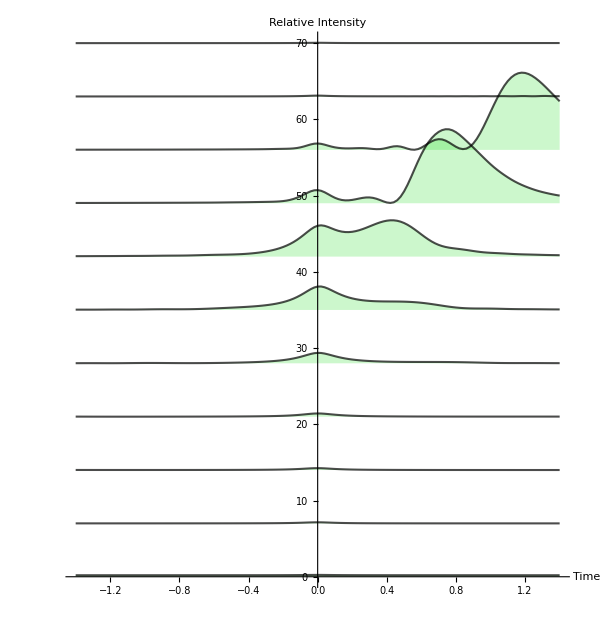

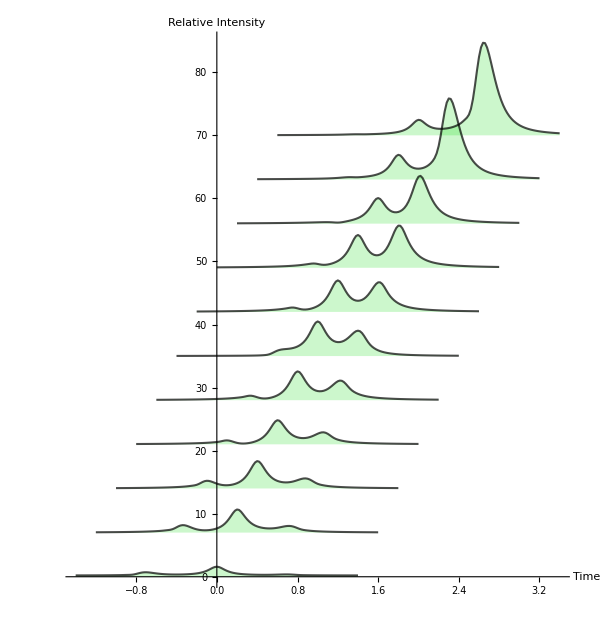

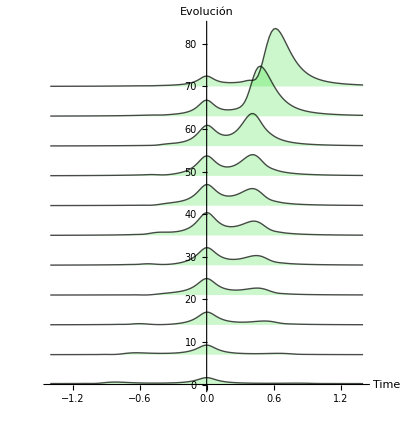

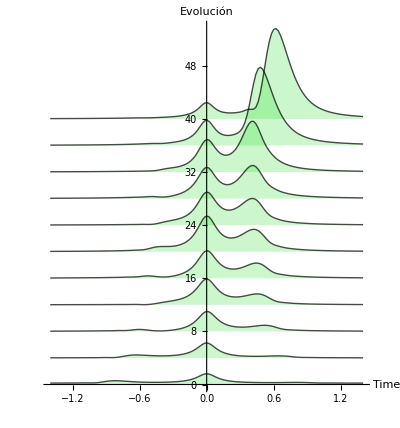

```mathematica
ListLinePlot[{
TranslationTransform[{0,70}][DTrace11],
TranslationTransform[{0,63}][DTrace10],
TranslationTransform[{0,56}][DTrace09],
TranslationTransform[{0,49}][DTrace08],
TranslationTransform[{0,42}][DTrace07],
TranslationTransform[{0,35}][DTrace06],
TranslationTransform[{0,28}][DTrace05],
TranslationTransform[{0,21}][DTrace04],
TranslationTransform[{0,14}][DTrace03],
TranslationTransform[{0,7}][DTrace02],
TranslationTransform[{0,0.2}][DTrace01]},
PlotStyle->Directive[ Black,Thickness[0.0025],Opacity[0.7]],
Filling->{1->70,2->63,3->56,4->49,5->42,6->35,7->28,8->21,9->14,10->7,11->0},
FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]],Axes->{True,False},AxesLabel->{"Time","Relative Intensity"},
ImageSize->600, AspectRatio->15/14]
```

### Animation

```mathematica
P1 = ListLinePlot[ParallelTable[{ω,S[Γ,ω*ν-ν,T,T0]},{ω,0,2*ν,(2*ν)/400}],PlotRange->{-0.1,16.2},Filling->0,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->{{14,2},{14,20}},PlotRangePadding->0,AspectRatio->1,FrameLabel->{Style["ω",16,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",16,FontFamily->"Times New Roman",Gray]},
 ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]],
GridLines->{{{1,Directive[Thickness[0.003],Red]},{(ν-Ωr)/ν,Directive[Thickness[0.003],Red]},{ (ν+Ωr)/ν,Directive[Thickness[0.003],Red]}},None}, PlotLabel->Style["Espectro Fisico EW   |ψ(0)⟩ = |g⟩ \n β = 0.1, Ω = 0.2, Γ = 0.1, t_0 = -200", 16, FontFamily->"Times New Roman", Black]];

P2 = Plot[{(Abs[alphaMas[t]]^2 )Exp[-2Re[alphaZ[t]]], Abs[Exp[- alphaZ[t]] ]^2}, {t, -150, 180}, FrameTicksStyle->{{20,2},{20,20}}, PlotStyle->{Thickness[0.003], Thickness[0.003], Directive[Dashed, Thickness[0.002], Orange, Opacity[0.85]], Directive[Dashed, Thickness[0.002], RGBColor[0,0.45,0.8], Opacity[0.85]]},PlotLegends-> {"P_(g → e)(t)", "P_(g → g)(t)"},AxesLabel-> {Style["t",14,GrayLevel[0.26]] , Style["P_g(t)",13, GrayLevel[0.26]]},AspectRatio->1, ImageSize->360,
GridLines->{{{T,Directive[Thickness[0.003],Darker[Red]]}},None},AxesOrigin->{-150,0},
PlotLabel->Style["Probabilidad de Transición, t = 16", 16, FontFamily->"Times New Roman", Black]];
```

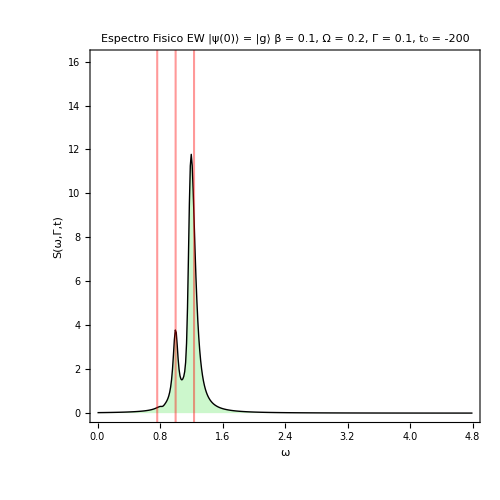

```mathematica
GraphicsRow[{P1,P2}, AspectRatio->Full,  ImageSize->1000, Alignment->Top]
```